# Intro to Mathematica:

### Wolfram Languages:

Capital letters to start all function names.

Function arguments are enclosed by square brackets [].

Lists, ranges, domains are enclosed by curly braces {}.

Shift+ Enter to run.

Multiplication use */space, example: a^b/a b. Don't use ab.

```mathematica
16 / 728
```

2/91

```mathematica
N[2/91]
```

0.021978

```mathematica
ScientificForm[0.021978]
```

2.1978×10^-2

```mathematica
Solve[x^2+5x+6=0,x]
```

Set::write: Tag Plus in 6+5 x+x^2 is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

```mathematica
j = 5
```

5

```mathematica
k = 4
```

4

```mathematica
l = j + k
```

9

```mathematica
Clear[j]
```

```mathematica
a = 23
```

23

```mathematica
b = 68
```

68

```mathematica
o = a * b
```

1564

```mathematica
Expand[(x-2)(x+2)]
```

-4+x^2

```mathematica
Apart[1/((1+x)(1+5x))]
```

-1/(4 (1+x))+5/(4 (1+5 x))

```mathematica
Factor[1+2x+x^2]
```

(1+x)^2

```mathematica
Factor[(x^10-y^10)]
```

(x-y) (x+y) (x^4-x^3 y+x^2 y^2-x y^3+y^4) (x^4+x^3 y+x^2 y^2+x y^3+y^4)

```mathematica
Factor[(1+x^10)]
```

(1+x^2) (1-x^2+x^4-x^6+x^8)

```mathematica
25/30
```

5/6

```mathematica
N[%]
```

0.833333

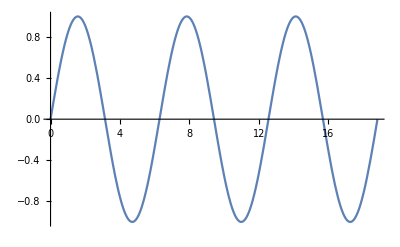

```mathematica
Plot[Sin[x], {x, 0, 6Pi}]
```

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2Pi}, PlotLabels -> "Expressions"]
```

-Graphics-

```mathematica
∑_(k=1)^n k
```

1/2 n (1+n)

```mathematica
f[x_] := x^2-3x
```

```mathematica
f[4]
```

4

```mathematica
Simplify[1/2Sin[2x]]
```

Cos[x] Sin[x]

```mathematica
A = {23, 56, 7, 88, 45}
```

{23,56,7,88,45}

```mathematica
Min[A]
```

7

```mathematica
Max[A]
```

88

```mathematica
∑_(k=1)^n k^2
```

1/6 n (1+n) (1+2 n)

```mathematica
f[y_] := y^3-4 y^2+5
```

```mathematica
f[3]
```

-4